# Google Form Parsing

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[_, _]]//Once
```

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\auto-paper\\google-form"]
```

C:\Users\sterg\Documents\GitHub\auto-paper\google-form

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"Palatino Linotype"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

```mathematica
responses=Import["C:\\Users\\sterg\\Documents\\GitHub\\auto-paper\\google-form\\scientific-document-tool-responses.csv"];
```

```mathematica
𝒬=responses⟦1⟧;
```

```mathematica
ℛ=responses⟦2;;⟧ᵀ;
{𝒜,𝒩,ℱ}=ℛ⟦#⟧&/@{2;;9,10;;12,13;;};(*answers, numbers, free response*)
𝒜=StringReplace[#,{"Box, Google Drive, etc."->"Box Google Drive etc.","Notability, and I"->"Notability and I"}]&/@𝒜;
𝒜=StringDelete[#,{" (python, MATLAB, etc.)"," and use \"Copy As\" (LaTeX, MathML, etc.)"," (e.g. tablesgenerator.com/latex_tables#)"," (e.g. Mathpix snipping tool)"," (i.e. your computer)"," but would like to know what is available.","Most frequently used is ","and I also use "}]&/@𝒜;
```

```mathematica
Subscript[𝒬, A]=StringReplace[𝒬⟦2;;9⟧,"Which computational programming language(s) do you use to analyze data?"->"Which languages do you use to analyze data?"];
Subscript[𝒬, N]=StringReplace[𝒬⟦10;;12⟧,{"How familiar are you with git version control software (e.g. GitHub Desktop, command line interface)"->"How familiar are you with git version control?","How familiar are you with generating figures using a coding language?"->"How familiar are you with generating figures via code?"}];
```

```mathematica
𝒞=Counts@Flatten@StringSplit[#,", "]&/@𝒜;
```

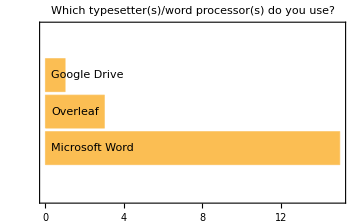
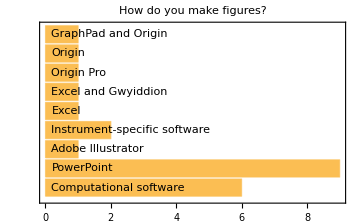
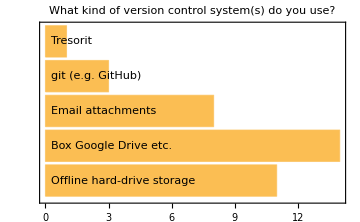
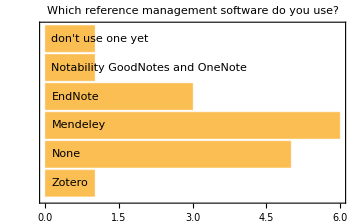
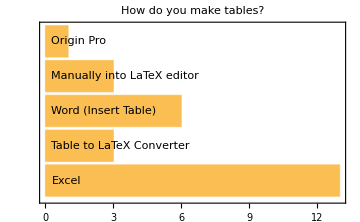
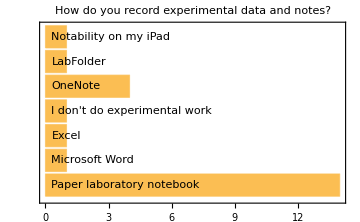
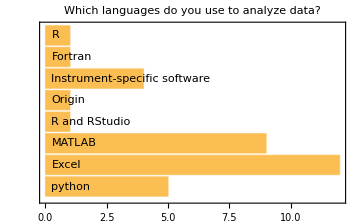
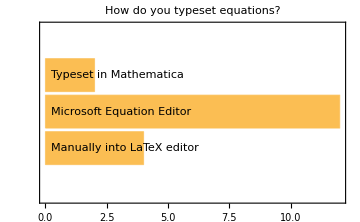
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
bc=MapThread[BarChart[#1,ChartLabels->Placed[Keys@#1,Left],BarOrigin->Left,ImageSize->Medium,Frame->True,PlotLabel->#2]&,{𝒞,Subscript[𝒬, A]}]//Multicolumn
```

```mathematica
Export["barchart-responses.png",bc]
```

barchart-responses.png

```mathematica
Counts/@𝒩
```

{<|3→4,1→8,4→1,2→3,5→1|>,<|1→10,3→3,2→3,5→1|>,<|3→5,1→7,2→4,5→1|>}

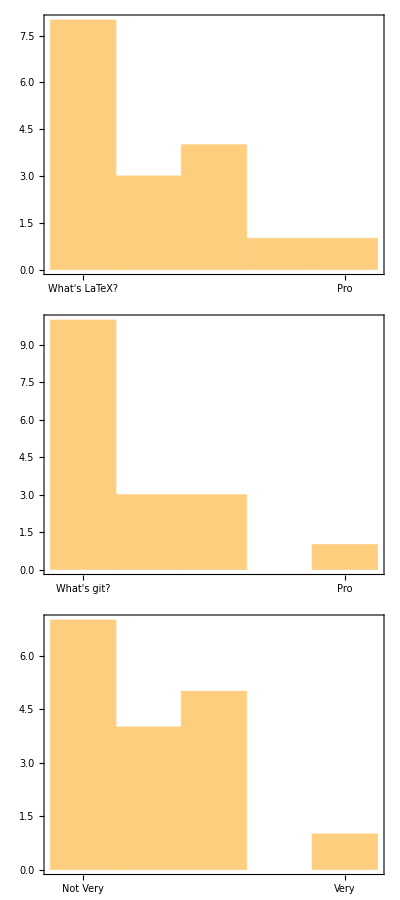

```mathematica
bc2=Grid[{MapThread[Histogram[#1,AspectRatio->1/4,ImageSize->Large,Frame->True,FrameTicks->{{Automatic,Automatic},{{{1,#2},{5,#3}},Automatic}},FrameLabel->{{None,None},{None,#4}}]&,{𝒩,{"What's LaTeX?","What's git?","Not Very"},{"Pro","Pro","Very"},Subscript[𝒬, N]}]}ᵀ]
```

```mathematica
Export["familiarity-responses.png",bc2]
```

familiarity-responses.png

# Code Graveyard

<|Microsoft Word→13,Microsoft Word, Overleaf→1,Overleaf→2,Microsoft Word, Google Drive→1|>

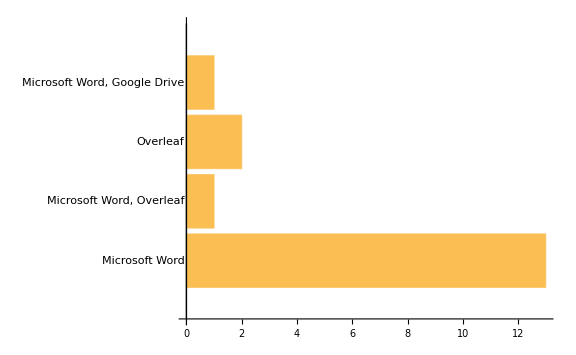
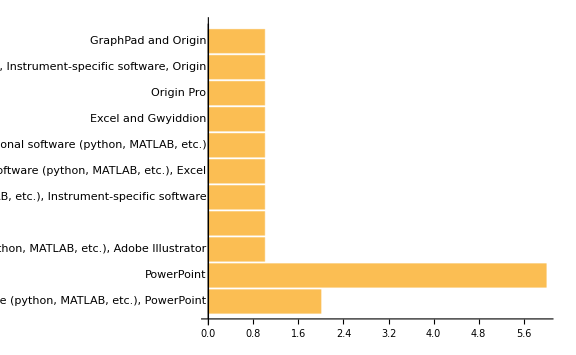
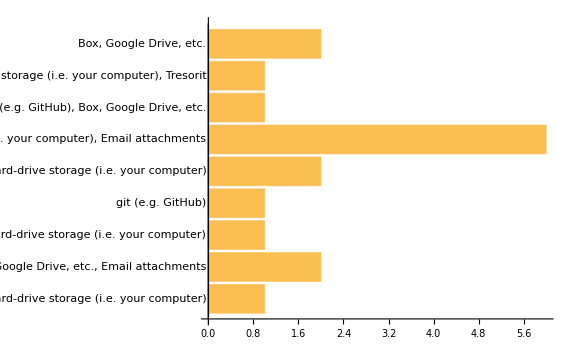
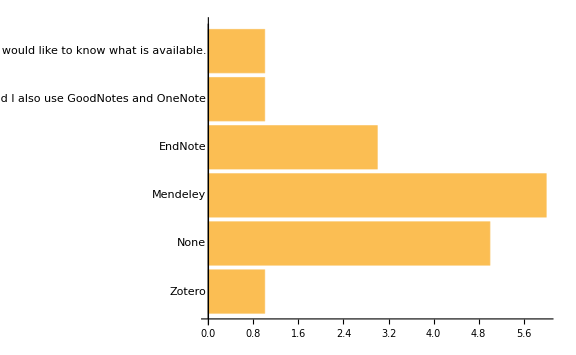
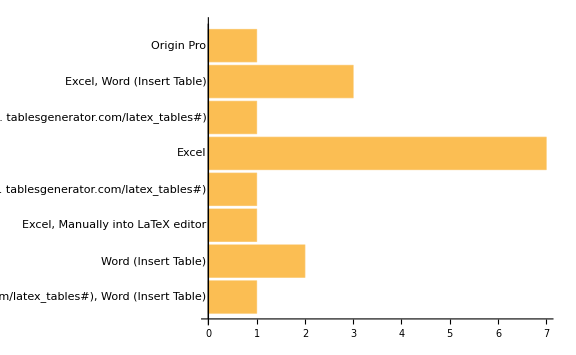
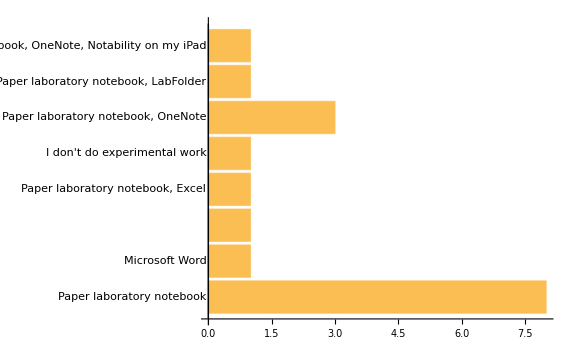
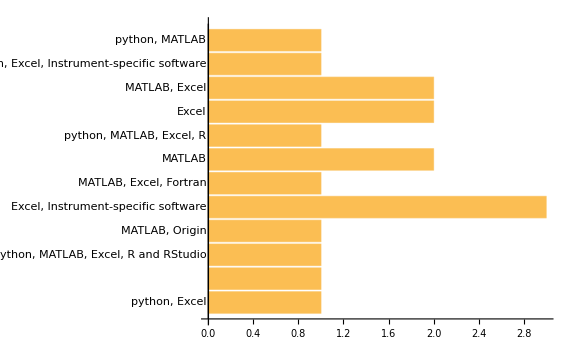
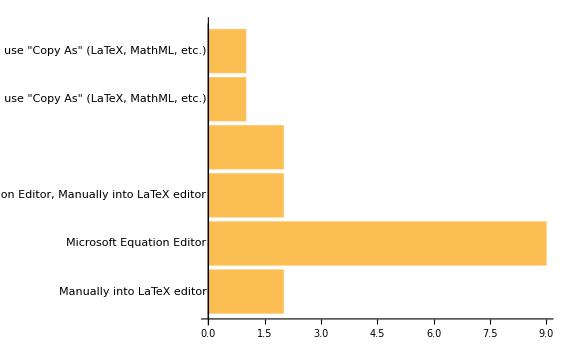
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
(*𝒞⟦1⟧*)
```

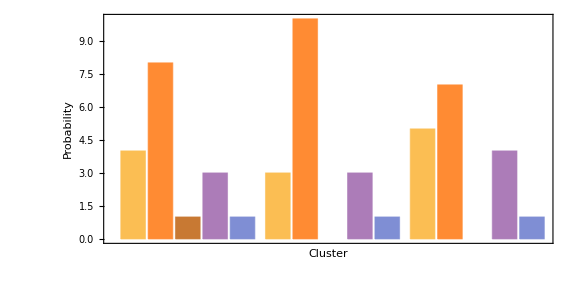

```mathematica
(*BarChart[Counts/@𝒩,Frame->{True,True,False,False},Axes->{False,True},PlotRangePadding->None,FrameStyle->Medium,FrameLabel->{"Cluster","Probability"},ImageSize->Large,AspectRatio->0.5]*)
```